```mathematica
rood[α_]:=RGBColor[1,0,0,α];
```

SetDelayed::write: Tag RGBColor in RGBColor[202/255, 22/85, 62/255][α_] is Protected.

## Remverliezen

Het doel van deze code is om interactief te kunnen zien wat de remverlieze zijn bij het afleggen van een bepaalde route. De gebruiker kan in het “Interactie”-veld een aantal punten op een vt-veld kiezen. Vervolgens worden alle versnellingen berekend, en de benodigde vermogens en totale input- en rem-energie.

### Code

#### Tekst-make-up

```mathematica
tekstrood[tekst_]:=TextCell[Style[tekst, FontSize->18,FontFamily->"Georgia",Red]];
tekst[tekst_,size_:18]:=TextCell[Style[tekst, FontSize->size,FontFamily->"Georgia",Black]];
tekstkleur[tekst_,kleur_,size_:18]:=TextCell[Style[tekst, FontSize->size,FontFamily->"Georgia",kleur]];
```

#### Snelheidomzetter

```mathematica
m2km[lijst_]:=({#[[1]],#[[2]]*3.6})&/@lijst (*Zet een lijst met {[s], [m/s]} om naar {[s], [km/h]}*);
km2m[lijst_]:=({#[[1]],#[[2]]/3.6})&/@lijst (*Zet een lijst met {[s], [km/h]} om naar {[s], [m/s]}*);
```

#### Integreerder

```mathematica
integreerder[lijst_]:=Module[{l,input,output,cumopp,cumopplist,dti,hs,os,ht,ot,oi},
l=Length[lijst];
input=0;
output=0;
cumopp=0;
cumopplist={lijst[[1]]};
For[i=1,i<l,i++,
dti=lijst[[i+1,1]]-lijst[[i,1]];
(*Gives time interval between point i and point i+1 (in s)*)
hs=lijst[[i,2]];
(*Gives the hight of the square part belonging to interval dti *)
os=dti*hs;
(*Gives the surface area of the square part*)
ht=lijst[[i+1,2]]-lijst[[i,2]];
(*Hight of the triangular part*)
ot=(1/2)*dti*ht;
(*Surface area of the triangular part*)
oi=os+ot;
(*Surface area per interval*)
If[oi<0,output+=oi,input+=oi];
(*For negative oi, the surface area is added to output. Otherwise it's addedto the input*)
cumopp+=oi;
(*Updates cumulative surface area*)
If[dti≠0,cumopplist=Append[cumopplist,{lijst[[i+1,1]],cumopp}]]
(*Adds the latest cumopp to the cumopplist list but only if dti ≠ 0*)
];
{input,output}];
```

```mathematica
integreerder[NEDC]*1000/3600
```

{2999.54,0}

```mathematica
32395./3
```

10798.3

#### NEDC

```mathematica
ECEdeel1={{0,0},{11,0},{15,15},{23,15},{28,0},{49,0},{61,32},{85,32},{96,0},{117,0},{143,50},{155,50},{163,35},{176,35}};
ECEdeel2=({#[[1]]+188,#[[2]]})&/@ECEdeel1;
ECEdeel3=({#[[1]]+188,#[[2]]})&/@ECEdeel2;
ECEdeel4=({#[[1]]+188,#[[2]]})&/@ECEdeel3;
EUDC=({#[[1]]+752,#[[2]]})&/@{{0,0},{20,0},{61,70},{111,70},{119,50},{188,50},{201,70},{251,70},{286,100},{316,100},{336,120},{346,120},{380,0},{400,0}};
NEDC=km2m[Join[ECEdeel1,ECEdeel2,ECEdeel3,ECEdeel4,EUDC]];(*NEDC parcour data met tijd in seconden en snelheid in m/s*)
```

```mathematica
NEDCs=integreerder[NEDC][[1]];(*Totale afstand NEDC parcour in meter*)
NEDCt=NEDC[[-1,1]];(*Totale tijd NEDC parcour in seconden*)
NEDCvavg=NEDCs/(NEDCt-5);(*Gemiddelde snelheid NEDC parcour in m/s, rekening houdend met 5 seconde opstarten en remmen*)
NEDCavg={{0,0},{5,NEDCvavg},{NEDCt-5,NEDCvavg},{NEDCt,0}};(*Zelfde afstand en tijd als het NEDC parcour maar nu met de gemiddelde snelheid (in m/s)*)
```

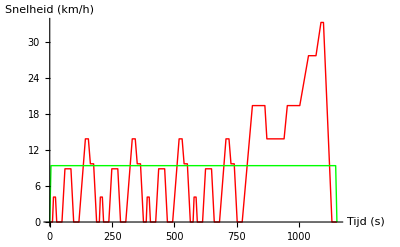

```mathematica
ListLinePlot[{NEDC,NEDCavg},AxesLabel->{"Tijd (s)","Snelheid (km/h)"},PlotStyle->{Red,Green}]
```

#### Vermogenfunctie

```mathematica
plijstf[vlijst_,massa_]:=Module[{alijst1,alijst2,alijst3,plijst},
(*Deze functie heeft als input een vt-lijst in {[s],[m/s]} format. Als output komt er lijst met ingaand vermogen uit.*)
alijst1=Table[(vlijst[[i,2]]-vlijst[[i-1,2]])/(vlijst[[i,1]]-vlijst[[i-1,1]]),{i,2,Length[vlijst]}];(*Berekend per interval de versnelling*)
alijst2=Table[{{vlijst[[i,1]],alijst1[[i]]},{vlijst[[i+1,1]],alijst1[[i]]}},{i,1,Length[alijst1]}];(*Construeert een nieuwe lijst op basis van alijst1 en zorgt dat elk interval de (constante) versnelling krijgt die erbij hoort*)
alijst3=Flatten[alijst2,1];(*Maakt een nette 2D-lijst van alijst2*)
plijst=Table[{alijst3[[i,1]],alijst3[[i,2]]*massa*vlijst[[Ceiling[i/2+0.1],2]]},{i,1,Length[alijst3]}](*Op basis van de alijst3 en de vlijst wordt hier een lijst met vermogens berekend (W/kg)*)];
```

#### Remverlies

```mathematica
padding={{60,60},{30,30}};(*Set padding voor de grafieken, nodig om uitlijning goed te krijgen*)
```

```mathematica
RemVerlies[vlijst_]:=
(*Deze functie heeft een lijst met {tijd,snelheid_in_km/h} als input*)
Module[{vtPlot,ptPlot,Ein,stot,output,verliesChart,Beschrijving},
(*Deze module heeft als input een lijst met vt-coordinaten nodig*)
vtPlot=ListLinePlot[m2km[vlijst],
ImageSize->1000,
PlotStyle->grijs,
PlotRange->{0,130},
AxesLabel->{"Tijd (s)","Snelheid (km/h)"},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14],
ImagePadding->padding,
AspectRatio->1/4];
ptPlot=ListLinePlot[({#[[1]],#[[2]]/1000})&/@plijstf[vlijst,1500],
Filling->Axis,
PlotRange->{-30,30},
FillingStyle->{Red,Green},
ImageSize->1000,
AxesLabel->{"Tijd (s)","Vermogen (kW)"},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14],
ImagePadding->padding,
AspectRatio->1/4];

Ein=integreerder[plijstf[vlijst,1500]][[1]];
stot=integreerder[vlijst][[1]];
Beschrijving=
Row[{
tekst["De totale afgelegde weg is "],
tekstrood[ToString[Round[stot/1000,0.1]]<>" kilometer"],
tekst[", en in totaal gaat "],
tekstrood[ToString[Round[Ein/10^6,0.01]]<>" MJ"],
tekst[" verloren in remverliezen."]}];

Grid[{{vtPlot},{ptPlot},{Beschrijving}}]
]
```

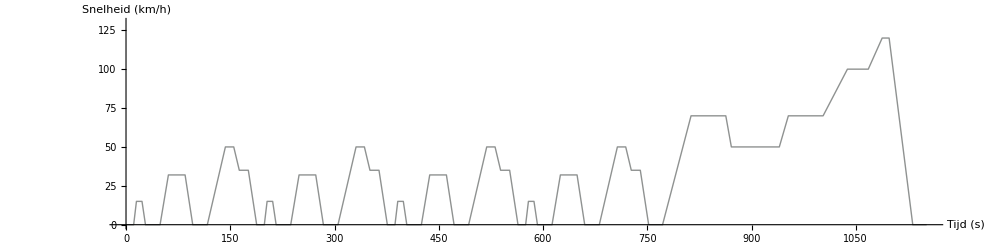
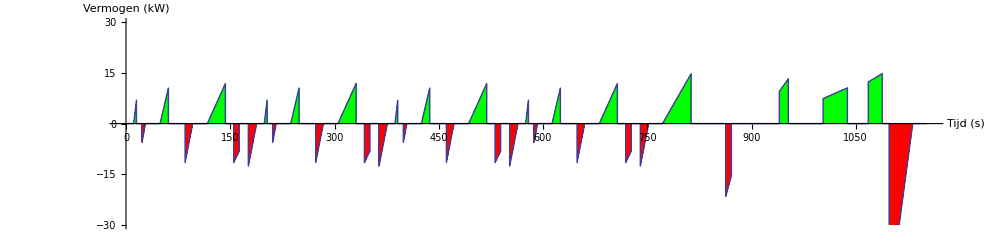
-Graphics-
-Graphics-
De totale afgelegde weg is 10.8 kilometer, en in totaal gaat 1.96 MJ verloren in remverliezen.

```mathematica
RemVerlies[NEDC]
```

#### Interface

```mathematica
NEDCfixed=RemVerlies[NEDC];
NEDCaverage=RemVerlies[NEDCavg];
Interactie=Manipulate[RemVerlies[km2m[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18,p19,p20,p21,p22,p23,p24,p25,p26,p27,p28,p29,p30,p31,p32,p33,p34,p35,p36,p37,p38,p39,p40,p41,p42,p43,p44,p45,p46,p47,p48,p49,p50,p51,p52,p53,p54,p55,p56,p57,p58,p59,p60,p61,p62,p63,p64,p65,p66,p67,p68,p69,p70}]],
{{p1,{0,0.}},Locator},{{p2,{11,0.}},Locator},{{p3,{15,15.}},Locator},{{p4,{23,15.}},Locator},{{p5,{28,0.}},Locator},{{p6,{49,0.}},Locator},{{p7,{61,32.}},Locator},{{p8,{85,32.}},Locator},{{p9,{96,0.}},Locator},{{p10,{117,0.}},Locator},{{p11,{143,50.}},Locator},{{p12,{155,50.}},Locator},{{p13,{163,35.}},Locator},{{p14,{176,35.}},Locator},{{p15,{188,0.}},Locator},{{p16,{199,0.}},Locator},{{p17,{203,15.}},Locator},{{p18,{211,15.}},Locator},{{p19,{216,0.}},Locator},{{p20,{237,0.}},Locator},{{p21,{249,32.}},Locator},{{p22,{273,32.}},Locator},{{p23,{284,0.}},Locator},{{p24,{305,0.}},Locator},{{p25,{331,50.}},Locator},{{p26,{343,50.}},Locator},{{p27,{351,35.}},Locator},{{p28,{364,35.}},Locator},{{p29,{376,0.}},Locator},{{p30,{387,0.}},Locator},{{p31,{391,15.}},Locator},{{p32,{399,15.}},Locator},{{p33,{404,0.}},Locator},{{p34,{425,0.}},Locator},{{p35,{437,32.}},Locator},{{p36,{461,32.}},Locator},{{p37,{472,0.}},Locator},{{p38,{493,0.}},Locator},{{p39,{519,50.}},Locator},{{p40,{531,50.}},Locator},{{p41,{539,35.}},Locator},{{p42,{552,35.}},Locator},{{p43,{564,0.}},Locator},{{p44,{575,0.}},Locator},{{p45,{579,15.}},Locator},{{p46,{587,15.}},Locator},{{p47,{592,0.}},Locator},{{p48,{613,0.}},Locator},{{p49,{625,32.}},Locator},{{p50,{649,32.}},Locator},{{p51,{660,0.}},Locator},{{p52,{681,0.}},Locator},{{p53,{707,50.}},Locator},{{p54,{719,50.}},Locator},{{p55,{727,35.}},Locator},{{p56,{740,35.}},Locator},{{p57,{752,0.}},Locator},{{p58,{772,0.}},Locator},{{p59,{813,70.}},Locator},{{p60,{863,70.}},Locator},{{p61,{871,50.}},Locator},{{p62,{940,50.}},Locator},{{p63,{953,70.}},Locator},{{p64,{1003,70.}},Locator},{{p65,{1038,100.}},Locator},{{p66,{1068,100.}},Locator},{{p67,{1088,120.}},Locator},{{p68,{1098,120.}},Locator},{{p69,{1132,0.}},Locator},{{p70,{1152,0.}},Locator},Paneled->False
];
```

### Interactie

```mathematica
Manipulate[
TabView[{"NEDC"->NEDCfixed,"NEDC (gemiddeld)"->NEDCaverage,"NEDC (variabel)"->Interactie},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14]],
SaveDefinitions->True,
Paneled->False]
```

## Lucht- en Rolwrijving

### Rolwrijving

```mathematica
Fwr[m_,crr_]:=m*crr*9.81;
Pwr[m_,crr_,v_]:=Fwr[m,crr]*v;
```

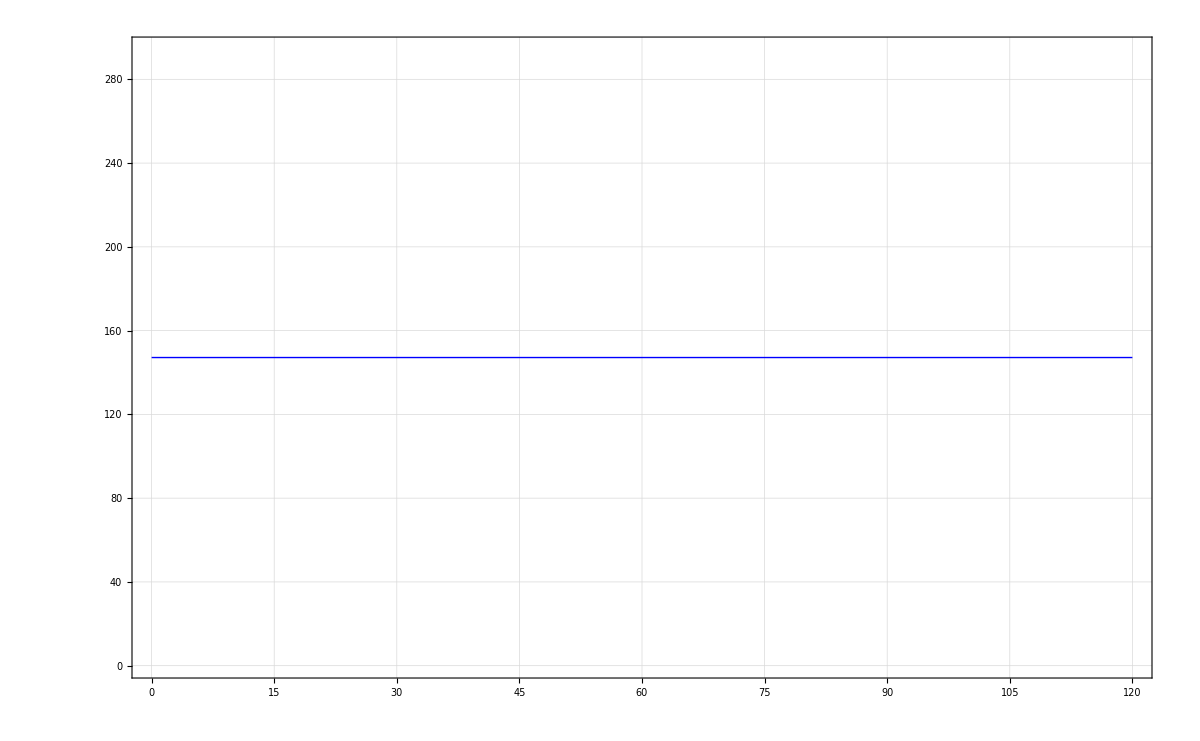
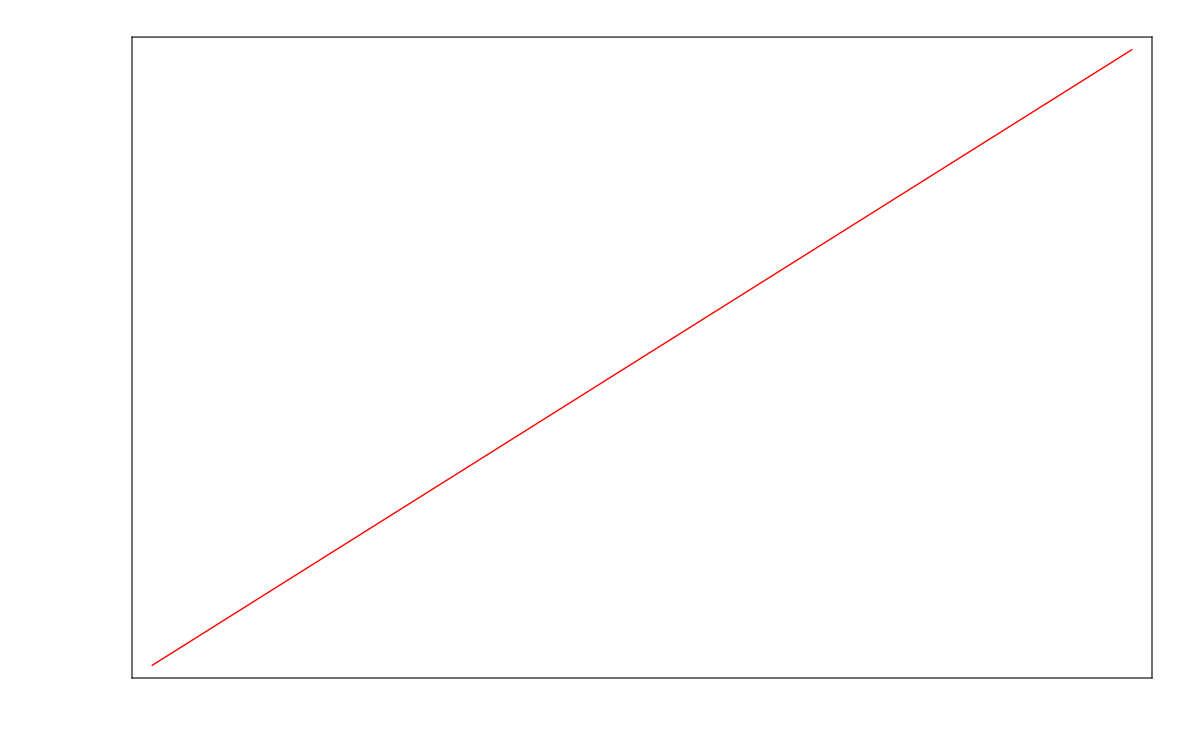
-Graphics--Graphics-Snelheid (km/h)Kracht (N)Vermogen (kW)Rolwrijving

```mathematica
r=1.5;
pad={{r*35,r*35},{r*25,r*10}};
Fplot=Plot[Fwr[1500,0.01],{v,0,120},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->r*16],
Frame->{True,True,True,False},
ImagePadding->pad,
GridLines->Automatic,
ImageSize->r*800,
PlotStyle->{Blue,Thick},
TicksStyle->Blue];
Pplot=Plot[Pwr[1500,0.01,km2m[v]]/1000,{v,0,120},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->r*16],
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
ImageSize->r*800,
ImagePadding->pad,
PlotStyle->{Red,Thick}];
Labeled[Overlay[{Fplot,Pplot}],{tekst["Snelheid (km/h)",r*16],tekstkleur["Kracht (N)",Blue,r*16],tekstkleur["Vermogen (kW)",Red,r*16],tekst["Rolwrijving",r*22]},{Bottom,Left,Right,Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Georgia"]]
```

```mathematica
Export["/Users/quintel/Dropbox/Quintel:Jonas Crossover/API testing/D3/Assets/Rolwrijving.jpg",Labeled[Overlay[{Fplot,Pplot}],{tekst["Snelheid (km/h)",r*16],tekstkleur["Kracht (N)",Blue,r*16],tekstkleur["Vermogen (kW)",Red,r*16],tekst["Rolwrijving",r*22]},{Bottom,Left,Right,Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Georgia"]]]
```

/Users/quintel/Dropbox/Quintel:Jonas Crossover/API testing/D3/Assets/Rolwrijving.jpg

### Luchtwrijving

```mathematica
Fwl[A_,cd_,v_]:=1/2 A*1.225*cd*v^2;
Pwl[A_,cd_,v_]:=Fwl[A,cd,v]*v;
```

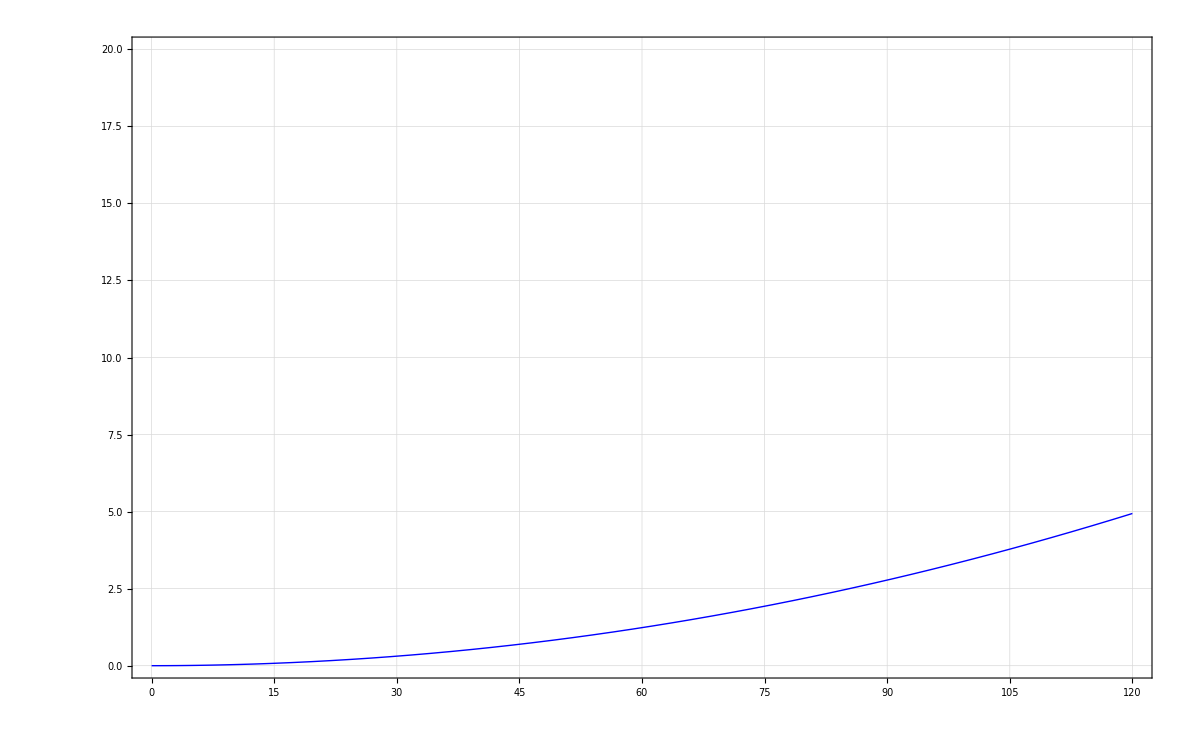
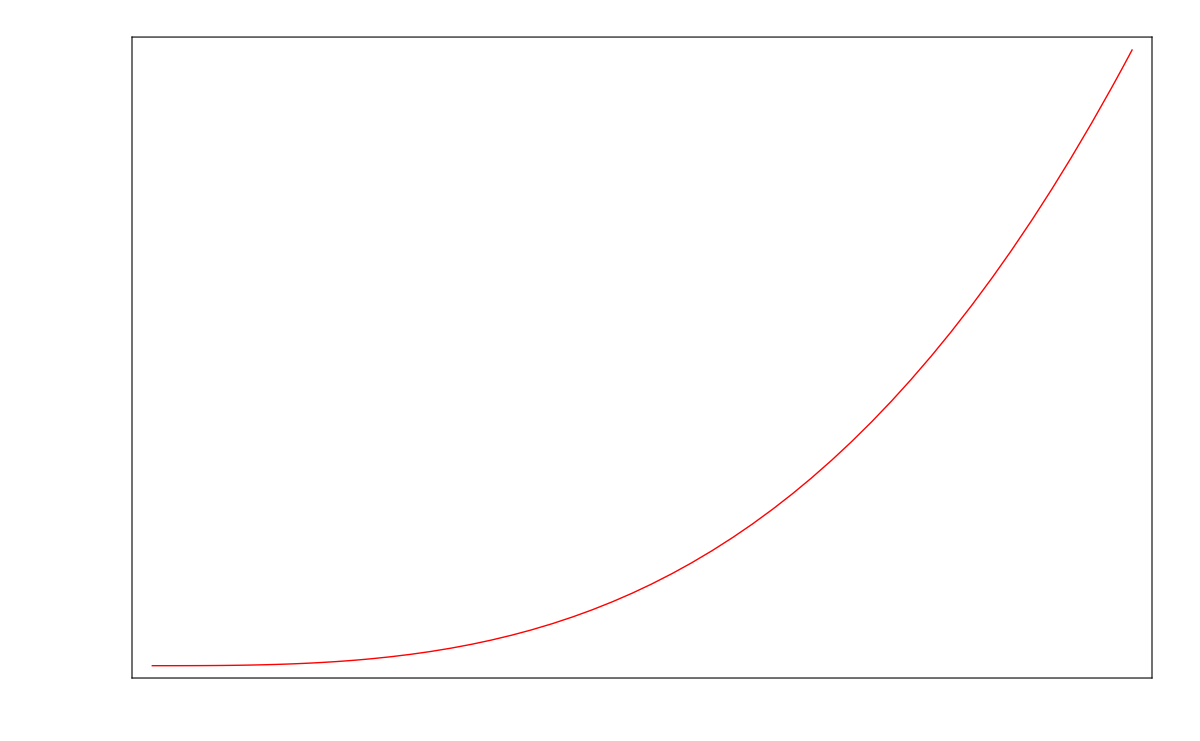
-Graphics--Graphics-Snelheid (km/h)Kracht (kN)Vermogen (kW)Luchtwrijving

```mathematica
r=1.5;
pad={{r*35,r*35},{r*25,r*10}};
Fplotw=Plot[Fwl[1.4,0.4,km2m[v]]/1000,{v,0,120},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->r*16],
Frame->{True,True,True,False},
ImagePadding->pad,
GridLines->Automatic,
ImageSize->r*800,
PlotRange->{0,20},
PlotStyle->{Blue,Thick},
TicksStyle->Blue];
Pplotw=Plot[Pwl[1.4,0.4,km2m[v]]/1000,{v,0,120},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->r*16],
Frame->{False,False,False,True},
FrameTicks->{None,None,None,All},
ImageSize->r*800,
ImagePadding->pad,
PlotStyle->{Red,Thick}];
Labeled[Overlay[{Fplotw,Pplotw}],{tekst["Snelheid (km/h)",r*16],tekstkleur["Kracht (kN)",Blue,r*16],tekstkleur["Vermogen (kW)",Red,r*16],tekst["Luchtwrijving",r*22]},{Bottom,Left,Right,Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Georgia"]]
```

```mathematica
Export["/Users/quintel/Dropbox/Quintel:Jonas Crossover/API testing/D3/Assets/Luchtwrijving.png",Labeled[Overlay[{Fplotw,Pplotw}],{tekst["Snelheid (km/h)",r*16],tekstkleur["Kracht (kN)",Blue,r*16],tekstkleur["Vermogen (kW)",Red,r*16],tekst["Luchtwrijving",r*22]},{Bottom,Left,Right,Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Georgia"]]]
```

/Users/quintel/Dropbox/Quintel:Jonas Crossover/API testing/D3/Assets/Luchtwrijving.png

### Lucht- en Rolwrijving samen

Het belangrijkste om te weten is de P(t) grafiek die hoort bij een bepaalde input v(t) grafiek. Net als bij de remverliezen zal de NEDC als uitgangspunt worden genomen. Je wilt afzonderlijk de lucht- en rolwrijving kunnen bekijken. Ik denk dat je moet kunnen kiezen tussen gestacked of achter elkaar, maar laten we beginnen met bij elkaar. Dat maakt het uitrekenen van het totale vermogensverlies makkelijker.

#### Energie per afstand

```mathematica
LuchtRol[Crr_,mc_,cd_,A_,η_]:=Module[{g,ρ,Prw,Plw,ErwM,ElwM,CrrD,mcD,cdD,AD,ErwMD,ElwMD,ηD},
g=9.81;
ρ=1.225;
CrrD=0.01;
mcD=1000;
cdD=0.33;
AD=0.8;
ηD=0.4;
Prw[v_]:=Crr mc g v;
Plw[v_]:=(ρ cd A v^3)/2;
ErwM[v_]:=1/η Crr mc g;(*De rolwrijving-energie die het kost om bij deze snelheid één meter te rijden (J)*)
ErwMD[v_]:=1/ηD CrrD mcD g;
ElwM[v_]:=1/η(ρ cd A v^2)/2;(*De luchtwrijving-energie die het kost om bij deze snelheid één meter te rijden (J)*)
ElwMD[v_]:=1/ηD(ρ cdD AD v^2)/2;
Plot[{ErwMD[v],ElwMD[v],ErwMD[v]+ElwMD[v],ErwM[v],ElwM[v],ErwM[v]+ElwM[v]},{v,0,50},
PlotStyle->{{Dotted,Gray},{Dotted,Gray},{Dotted,Black},{Black},{Black},{Red}},
AxesLabel->{"Snelheid (m/s)","Energie per afstand (J/m)"},
PlotRange->{0,3000},
ImageSize->500]]
```

```mathematica
LuchtRolInteractie=Manipulate[LuchtRol[Crr,mc,cd,A,η],
{{Crr,0.01,"Rolwrijvingcoëfficiënt"},0,0.02},
{{mc,1000,"Gewicht auto (kg)"},50,5000},
{{cd,0.33,"Luchtwrijvingcoëfficiënt"},0,1},
{{A,0.8,"Frontaal oppervlak (m^2)"},0.2,2},
{{η,0.4,"Efficiëntie Motor"},0,1},
Button["Hummer",{A=2,mc=2000,η=0.2,Crr=0.015,cd=0.5}],
Button["Prius",{A=0.7,mc=800,η=0.45,Crr=0.015,cd=0.25}],SaveDefinitions->True];
```

```mathematica
LuchtRolParcour[Crr_,mc_,cd_,A_,η_,vlijst_]:=Module[{g,ρ,Prw,Plw,ErwM,ElwM,CrrD,mcD,cdD,AD,ErwMD,ElwMD,ηD,vv,alijst1,PrwD,PlwD,Pplot,vplot},
g=9.81;
ρ=1.225;
CrrD=0.01;
mcD=1000;
cdD=0.33;
AD=0.8;
ηD=0.4;
alijst1=Table[(vlijst[[i,2]]-vlijst[[i-1,2]])/(vlijst[[i,1]]-vlijst[[i-1,1]]),{i,2,Length[vlijst]}];
vv[t_]:=Piecewise[Table[{
alijst1[[i]]*(t-vlijst[[i,1]])+vlijst[[i,2]],
vlijst[[i,1]]≤t≤vlijst[[i+1,1]]
},{i,1,Length[alijst1]}]];
Prw[t_]:=1/η Crr mc g vv[t];
Plw[t_]:=1/η(ρ cd A vv[t]^3)/2;
PrwD[t_]:=1/ηD CrrD mcD g vv[t];
PlwD[t_]:=1/ηD(ρ cdD AD vv[t]^3)/2;
Pplot=Plot[{PrwD[t],PrwD[t]+PlwD[t],Prw[t],Prw[t]+Plw[t]},{t,0,vlijst[[-1,1]]},
PlotStyle->{{Dotted,Gray},{Dotted,Gray},{Black},{Red}},
AxesLabel->{"Tijd (s)","Vermogen (W)"},
PlotRange->{0,10000},
ImageSize->400,
Filling->{4->3,3->Axis}];
vplot=ListLinePlot[vlijst,ImageSize->400,AxesLabel->{"Tijd (s)","Snelheid (m/s)"},PlotRange->{0,40}];
Grid[{{vplot},{Pplot}}]]
```

```mathematica
LuchtRolParcourInteractie=Manipulate[LuchtRolParcour[Crr,mc,cd,A,η,{p1,p2,p3,p4,p5}],
{{p1,{0,0}},Locator},
{{p2,{10,20}},Locator},
{{p3,{30,25}},Locator},
{{p4,{80,25}},Locator},
{{p5,{100,0}},Locator},
{{Crr,0.01,"Rolwrijvingcoëfficiënt"},0,0.02},
{{mc,1000,"Gewicht auto (kg)"},50,5000},
{{cd,0.33,"Luchtwrijvingcoëfficiënt"},0,1},
{{A,0.8,"Frontaal oppervlak (m^2)"},0.2,2},
{{η,0.4,"Efficiëntie Motor"},0,1},
Button["Hummer",{A=2,mc=2000,η=0.2,Crr=0.015,cd=0.5}],
Button["Prius",{A=0.7,mc=800,η=0.45,Crr=0.015,cd=0.25}],
SaveDefinitions->True];
```

#### Efficiënte LuchtRol

Deze module is relatief snel doordat er twee versie zijn: een versie die grof update en geen integratie doet. En een versie die wat langer duurt, maar wel een mooi resultaat weergeeft en verschillende integralen uitrekent.

```mathematica
LuchtRolEff0[vlijst_,m_:1500,crr_:0.01,cd_:0.4,A_:1.4,η_:0.3]:=Module[{alijst,ρ,g,Pwl,Pwr,Ptot,ti,tf,Etot,Ltot,Rtot,Stot,Pplot,vtPlot,Beschrijving,Beschrijving2},
ρ=1.225;
g=9.81;
vtijd=Timing[v=Interpolation[vlijst,InterpolationOrder->1]][[1]];
Pwl[t_]:=1/2 A*ρ*cd*v[t]^3;
Pwr[t_]:=m*crr*g*v[t];
Ptot[t_]:=Pwl[t]+Pwr[t];
ti=vlijst[[1,1]];
tf=vlijst[[-1,1]];
vplottijd=Timing[vtPlot=ListLinePlot[m2km[vlijst],
ImageSize->1000,
PlotStyle->Gray,
PlotRange->{0,130},
AxesLabel->{"Tijd (s)","Snelheid (km/h)"},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14],
ImagePadding->padding,
AspectRatio->1/4]][[1]];

pplottijd=Timing[Pplot=Plot[{Pwl[t]/1000,Pwr[t]/1000,Ptot[t]/1000},{t,ti,tf},
PlotStyle->{{Dotted,Blue},{Dotted,Black},{Red}},
Filling->{3->Axis},
FillingStyle->CTOTF,
PlotRange->{0,20},
ImageSize->1000,
PlotPoints->100,
MaxRecursion->0,
AxesLabel->{"Tijd (s)","Vermogen (kW)"},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14],
ImagePadding->padding,
AspectRatio->1/4]][[1]];

Beschrijving=
Row[{
tekst["Updaten… "]}];
Beschrijving2=
Row[{
tekstkleur["(...)",RGBColor[0,0,0,0.3]]}];

Grid[{{vtPlot},{Pplot},{Beschrijving},{Beschrijving2}}]];
```

```mathematica
LuchtRolEff[vlijst_,m_:1500,crr_:0.01,cd_:0.4,A_:1.4,η_:0.3]:=Module[{alijst,ρ,g,Pwl,Pwr,Ptot,ti,tf,Etot,Ltot,Rtot,Stot,Pplot,vtPlot,Beschrijving,Beschrijving2},
ρ=1.225;
g=9.81;
v=Interpolation[vlijst,InterpolationOrder->1];
Pwl[t_]:=1/2 A*ρ*cd*v[t]^3;
Pwr[t_]:=m*crr*g*v[t];
Ptot[t_]:=Pwl[t]+Pwr[t];
ti=vlijst[[1,1]];
tf=vlijst[[-1,1]];
Ltot=NIntegrate[Pwl[t],{t,ti,tf}];
Rtot=NIntegrate[Pwr[t],{t,ti,tf}];
Etot=NIntegrate[Ptot[t],{t,ti,tf}];
Stot=NIntegrate[v[t],{t,ti,tf}];

vtPlot=ListLinePlot[m2km[vlijst],
ImageSize->1000,
PlotRange->{0,130},
PlotStyle->Gray,
AxesLabel->{"Tijd (s)","Snelheid (km/h)"},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14],
ImagePadding->padding,
AspectRatio->1/4];

Pplot=Plot[{Pwl[t]/1000,Pwr[t]/1000,Ptot[t]/1000},{t,ti,tf},
PlotStyle->{{Dotted,Blue},{Dotted,Black},{Red}},
Filling->{3->Axis},
FillingStyle->CTOTF,
PlotRange->{0,20},
ImageSize->1000,
AxesLabel->{"Tijd (s)","Vermogen (kW)"},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14],
ImagePadding->padding,
AspectRatio->1/4];

Beschrijving=
Row[{
tekst["De totale afgelegde weg is "],
tekstrood[ToString[Round[Stot/1000,0.1]]<>" kilometer"],
tekst[", en in totaal gaat "],
tekstrood[ToString[Round[Etot/10^6,0.01]]<>" MJ"],
tekst[" verloren in lucht- en rolwrijving."]}];
Beschrijving2=
Row[{
tekstkleur["(hiervan is ",RGBColor[0,0,0,0.3]],
tekstkleur[ToString[Round[Ltot/10^6,0.01]]<>" MJ luchtwrijving",RGBColor[1,0,0,0.4]],
tekstkleur[", en ",RGBColor[0,0,0,0.3]],
tekstkleur[ToString[Round[Rtot/10^6,0.01]]<>" MJ rolwrijving",RGBColor[1,0,0,0.4]],
tekstkleur[")",RGBColor[0,0,0,0.3]]}];

Grid[{{vtPlot},{Pplot},{Beschrijving},{Beschrijving2}}]];
```

#### Interactie van de efficiëntie LuchtRol

```mathematica
NEDCfixedLR=LuchtRolEff[NEDC];
NEDCaverageLR=LuchtRolEff[NEDCavg];
InteractieLR=Manipulate[ControlActive[LuchtRolEff0[km2m[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18,p19,p20,p21,p22,p23,p24,p25,p26,p27,p28,p29,p30,p31,p32,p33,p34,p35,p36,p37,p38,p39,p40,p41,p42,p43,p44,p45,p46,p47,p48,p49,p50,p51,p52,p53,p54,p55,p56,p57,p58,p59,p60,p61,p62,p63,p64,p65,p66,p67,p68,p69,p70}]],LuchtRolEff[km2m[{p1,p2,p3,p4,p5,p6,p7,p8,p9,p10,p11,p12,p13,p14,p15,p16,p17,p18,p19,p20,p21,p22,p23,p24,p25,p26,p27,p28,p29,p30,p31,p32,p33,p34,p35,p36,p37,p38,p39,p40,p41,p42,p43,p44,p45,p46,p47,p48,p49,p50,p51,p52,p53,p54,p55,p56,p57,p58,p59,p60,p61,p62,p63,p64,p65,p66,p67,p68,p69,p70}]]],
{{p1,{0,0.}},Locator},{{p2,{11,0.}},Locator},{{p3,{15,15.}},Locator},{{p4,{23,15.}},Locator},{{p5,{28,0.}},Locator},{{p6,{49,0.}},Locator},{{p7,{61,32.}},Locator},{{p8,{85,32.}},Locator},{{p9,{96,0.}},Locator},{{p10,{117,0.}},Locator},{{p11,{143,50.}},Locator},{{p12,{155,50.}},Locator},{{p13,{163,35.}},Locator},{{p14,{176,35.}},Locator},{{p15,{188,0.}},Locator},{{p16,{199,0.}},Locator},{{p17,{203,15.}},Locator},{{p18,{211,15.}},Locator},{{p19,{216,0.}},Locator},{{p20,{237,0.}},Locator},{{p21,{249,32.}},Locator},{{p22,{273,32.}},Locator},{{p23,{284,0.}},Locator},{{p24,{305,0.}},Locator},{{p25,{331,50.}},Locator},{{p26,{343,50.}},Locator},{{p27,{351,35.}},Locator},{{p28,{364,35.}},Locator},{{p29,{376,0.}},Locator},{{p30,{387,0.}},Locator},{{p31,{391,15.}},Locator},{{p32,{399,15.}},Locator},{{p33,{404,0.}},Locator},{{p34,{425,0.}},Locator},{{p35,{437,32.}},Locator},{{p36,{461,32.}},Locator},{{p37,{472,0.}},Locator},{{p38,{493,0.}},Locator},{{p39,{519,50.}},Locator},{{p40,{531,50.}},Locator},{{p41,{539,35.}},Locator},{{p42,{552,35.}},Locator},{{p43,{564,0.}},Locator},{{p44,{575,0.}},Locator},{{p45,{579,15.}},Locator},{{p46,{587,15.}},Locator},{{p47,{592,0.}},Locator},{{p48,{613,0.}},Locator},{{p49,{625,32.}},Locator},{{p50,{649,32.}},Locator},{{p51,{660,0.}},Locator},{{p52,{681,0.}},Locator},{{p53,{707,50.}},Locator},{{p54,{719,50.}},Locator},{{p55,{727,35.}},Locator},{{p56,{740,35.}},Locator},{{p57,{752,0.}},Locator},{{p58,{772,0.}},Locator},{{p59,{813,70.}},Locator},{{p60,{863,70.}},Locator},{{p61,{871,50.}},Locator},{{p62,{940,50.}},Locator},{{p63,{953,70.}},Locator},{{p64,{1003,70.}},Locator},{{p65,{1038,100.}},Locator},{{p66,{1068,100.}},Locator},{{p67,{1088,120.}},Locator},{{p68,{1098,120.}},Locator},{{p69,{1132,0.}},Locator},{{p70,{1152,0.}},Locator},Paneled->False,ContinuousAction->False,SaveDefinitions->True
];
```

```mathematica
TabView[{"NEDC"->NEDCfixedLR,"NEDC (gemiddeld)"->NEDCaverageLR,"NEDC (variabel)"->InteractieLR},
LabelStyle->Directive[FontFamily->"Georgia",FontSize->14]]
```

123

Hier moet nog iets van een legenda bij